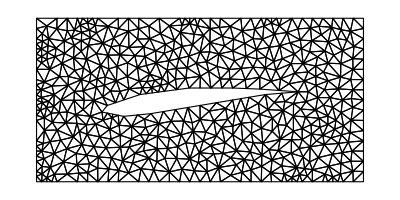

```mathematica
(* Start of given code *)
wing = Polygon[{{-18,-2.2},{-14,-3},{-9,-2.5},{0,-1},{12,1},{18,1.5},{11,2},{6,2.2},{-2,2.2},{-11,1},{-17,-1},{-18,-2.2}}];
rectangle = Rectangle[{-30,-15},{30,15}];
reg = RegionDifference[rectangle,wing];
Needs["NDSolve`FEM`"]
mesh=ToElementMesh[DiscretizeRegion[reg],MaxCellMeasure->3,"MeshOrder"-> 1];
mesh["Wireframe"]
(*Remove semicolon for more detailed mesh*)
Show[mesh["Wireframe"["MeshElementIDStyle"->Red]],mesh["Wireframe"["MeshElement"->"PointElements","MeshElementIDStyle"->Blue]]];
nodes = mesh["Coordinates"];
elements = mesh["MeshElements"][[1,1]];
boundary =Flatten[mesh["BoundaryElements"][[1,1]]];
boundary=DeleteDuplicates[boundary];
Subscript[Γ, els]=N[{{-18,-2.2},{-14,-3},{-9,-2.5},{0,-1},{12,1},{18,1.5},{11,2},{6,2.2},{-2,2.2},{-11,1},{-17,-1},{-18,-2.2}}];
upp = Cases[nodes[[boundary]],{_,y_}/;y== 15.];
low = Cases[nodes[[boundary]],{_,y_}/;y== -15.];
For[i=1,i≤ Length[low],i++,
AppendTo[Subscript[Γ, els],low⟦i⟧]; 
];
For[i=1,i≤ Length[upp],i++,
AppendTo[Subscript[Γ, els],upp⟦i⟧]; 
];
Subscript[Γ, in]=Cases[nodes⟦boundary⟧,{x_,_}/;x== -30.];
Subscript[Γ, out]=Cases[nodes⟦boundary⟧,{x_,_}/;x== 30.];inElems=Table[{Position[nodes,Sort[Subscript[Γ, in]]⟦i⟧]⟦1,1⟧,Position[nodes,Sort[Subscript[Γ, in]]⟦i+1⟧]⟦1,1⟧},{i,1,Length[Subscript[Γ, in]]-1}];
outNodes = Table[Position[nodes, Subscript[Γ, out]⟦i⟧]⟦1,1⟧,{i,1,Length[Subscript[Γ, out]]}];
(* End of given code *)
```

```mathematica
(* Standard basis functions, i.e. shape functions *)
Subscript[ψ, 0][{ξ_,η_}]:=1-ξ-η
Subscript[ψ, 1][{ξ_,η_}]:=ξ
Subscript[ψ, 2][{ξ_,η_}]:=η
gradψ=Transpose@Grad[{Subscript[ψ, 0][{ξ,η}],Subscript[ψ, 1][{ξ,η}],Subscript[ψ, 2][{ξ,η}]},{ξ,η}];
gradψT=Transpose@gradψ;

(* The Jacobian and Jacobian inverse *)
(* Here we utilise the fact that R^2 vectors are represented as lists and we can directly get their "transpose" by using the list *)
J[nodes_,element_]:={
nodes⟦element⟦2⟧⟧-nodes⟦element⟦1⟧⟧,
nodes⟦element⟦3⟧⟧-nodes⟦element⟦1⟧⟧}
B[nodes_,element_]:={
{nodes⟦element⟦3⟧⟧⟦2⟧-nodes⟦element⟦1⟧⟧⟦2⟧,nodes⟦element⟦1⟧⟧⟦2⟧-nodes⟦element⟦2⟧⟧⟦2⟧},
{nodes⟦element⟦1⟧⟧⟦1⟧-nodes⟦element⟦3⟧⟧⟦1⟧,nodes⟦element⟦2⟧⟧⟦1⟧-nodes⟦element⟦1⟧⟧⟦1⟧}}

(* The local stiffness matrix *)
(* Formally, we would have to do something like this 
localStiffness[nodes_, element_]:=
1/(Det@J[nodes,element])NIntegrate[gradψT.(Transpose@B[nodes,element]).B[nodes,element].gradψ,{ξ,0,1},{η,0,1-ξ}]*)
(* However the integrand is constant so we just need to multiply it by the area of the standard triangle, which is 1/2 *)
localStiffness[nodes_, element_]:=
0.5/(Det@J[nodes,element])gradψT.Transpose@B[nodes,element].B[nodes,element].gradψ

(* The function that assebles the global stiffness matrix *)
assembleMatrix[nodes_,elements_]:=(
globalMatrix = Table[Table[0,Length[nodes]],Length[nodes]];
For[k=1,k≤Length[elements],k++,
element = elements⟦k⟧;
stiffness=localStiffness[nodes,element];
For[i=1,i≤3,i++,
For[j=1,j≤3,j++,
globalMatrix⟦element⟦i⟧,element⟦j⟧⟧+=stiffness⟦i, j⟧;
];
];
];

(* We should now take into account that some of the coefficients will have to be 0 to ensure the boundary condition of u=0 *)
For[i=1,i≤Length@outNodes,i++,
globalMatrix⟦outNodes⟦i⟧⟧=Table[0,{j,1,Length@nodes}];
For[j=1,j≤Length@nodes,j++,
globalMatrix⟦j,outNodes⟦i⟧⟧=0;
];
globalMatrix⟦outNodes⟦i⟧,outNodes⟦i⟧⟧=1;
];

globalMatrix
)

loadVector=Table[0,Length@nodes];
For[k=1,k≤Length@inElems,k++,
{i,j}=inElems⟦k⟧;
loadVector⟦i⟧+=0.5Norm[nodes⟦i⟧-nodes⟦j⟧];
loadVector⟦j⟧+=0.5Norm[nodes⟦i⟧-nodes⟦j⟧];
];

(* Where u=0 we should have loadVector = 0 *)
For[k=1,k≤Length@outNodes,k++,
loadVector⟦outNodes⟦k⟧⟧=0;
];
```

$Aborted[]

-Graphics-

35.1624 η+33.5753 (1-η-ξ)+34.1013 ξ

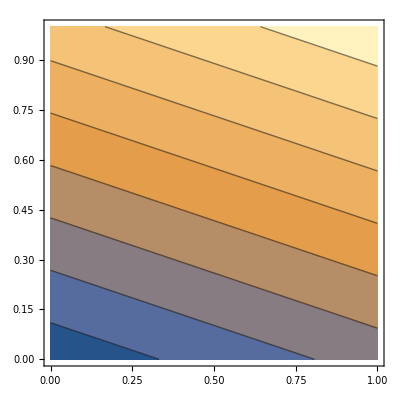

```mathematica
Subscript[M, 1]=assembleMatrix[nodes,elements];
b=loadVector;
q=LinearSolve[Subscript[M, 1],b];
Show[
Table[
ContourPlot[
q⟦elements⟦k⟧⟦1⟧⟧Subscript[ψ, 0][{ξ,η}]+q⟦elements⟦k⟧⟦2⟧⟧Subscript[ψ, 1][{ξ,η}]+q⟦elements⟦k⟧⟦3⟧⟧Subscript[ψ, 2][{ξ,η}],
{ξ,0,1},{η,0,1}],
{k,1,Length@elements}]
]
```